# Лабораторная работа №1

## Группы на плоскости

Мат. моделирование динамических процессов 2
БГУ, ММФ, 4 курс, 7 семестр
специальность Компьютерная математика и системный анализ
сентябрь 2022
проф. Громак В.И., ассист. Кухарев А.Л.
работу выполнил 
студент 4 курса 5a группы ММФ БГУ
Кирилло Дмитрий

## Задание 1

Говорят, что семейство преобразований какого - то множества образует группу, если это семейство замкнуто относительно композиции (т . е . содержит композицию любых двух входящих в него преобразований) и относительно взятия обратного преобразования .

### Функция для тождественного преобразования

```mathematica
ClearAll[identityFunction];
identityFunction[T_,a_]:=(Quiet@First[Solve[MapThread[#1==#2&,{T[a][{x,y}],{x,y}}],a,Reals]]//Simplify)⟦1⟧
```

### Функция для обратного преобразования

```mathematica
ClearAll[inverseFunction];
inverseFunction[T_,a_]:=(Quiet@First[Solve[MapThread[#1==#2&,{Composition[T[b],T[a]][{x,y}],{x,y}}],b,Reals]]//Simplify)⟦1⟧
```

### Функция для композиции

```mathematica
ClearAll[compositionFunction];
compositionFunction[T_,a_,b_]:=(Quiet@First[Solve[MapThread[#1==#2&,{Composition[T[b],T[a]][{x,y}],T[c][{x,y}]}],c,Reals]]//Simplify)⟦1⟧
```

### Перенос вдоль прямой

```mathematica
ClearAll[Ta1];
Ta1[a_][{x_,y_}]:={x+l a,y+k a}
```

```mathematica
identityFunction[Ta1,a]
```

a→0

```mathematica
inverseFunction[Ta1,a]
```

b→-a

```mathematica
compositionFunction[Ta1,a,b]//Simplify
```

c→a+b

```mathematica
Ta1[a][(Composition[Ta1[b],Ta1[c]][{x,y}])]==(Composition[Ta1[a],Ta1[b]])[Ta1[c][{x,y}]]
```

True

### Вращение

```mathematica
ClearAll[Ta2];
Ta2[a_][{x_,y_}]:={x Cos[a]+y Sin[a],-x Sin[a]+y Cos[a]}
```

```mathematica
Solve[identityFunction[Ta2,a],a]
```

{{a→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[(x^2-y^2)/(x^2+y^2),(2 x y)/(x^2+y^2)]+2 π C[1], C[1]∈ℤ]}}

```mathematica
Solve[inverseFunction[Ta2,a],b]
```

{{b→ConditionalExpression[-a+2 π C[1], C[1]∈ℤ]},{b→ConditionalExpression[-a+ArcTan[(x^2-y^2)/(x^2+y^2),(2 x y)/(x^2+y^2)]+2 π C[1], C[1]∈ℤ]}}

```mathematica
Solve[compositionFunction[Ta2,a,b],c]//Simplify
```

{{c→ConditionalExpression[ArcTan[(x^2 Cos[a+b]+x y Sin[a+b]-√(y^2 (y Cos[a+b]-x Sin[a+b])^2))/(x^2+y^2),(x y^2 Cos[a+b]+y^3 Sin[a+b]+x √(y^2 (y Cos[a+b]-x Sin[a+b])^2))/(y (x^2+y^2))]+2 π C[1], C[1]∈ℤ]},{c→ConditionalExpression[ArcTan[(x^2 Cos[a+b]+x y Sin[a+b]+√(y^2 (y Cos[a+b]-x Sin[a+b])^2))/(x^2+y^2),(x y^2 Cos[a+b]+y^3 Sin[a+b]-x √(y^2 (y Cos[a+b]-x Sin[a+b])^2))/(y (x^2+y^2))]+2 π C[1], C[1]∈ℤ]}}

```mathematica
Ta2[a][(Composition[Ta2[b],Ta2[c]][{x,y}])]==(Composition[Ta2[a],Ta2[b]])[Ta2[c][{x,y}]]
```

True

### Преобразование Лоренца

В данном задании решения для преобразования Лоренца находятся только на комплексном множестве. Соответственно, чтобы увидеть это решение, изначальные функции, которые были заданы в начале лабораторной работе, нужно немного изменить: поменять решения со множества Reals на Complexes

```mathematica
ClearAll[identityFunctionComplex];
identityFunctionComplex[T_,a_]:=(Quiet@First[Solve[MapThread[#1==#2&,{T[a][{x,y}],{x,y}}],a,Complexes]]//Simplify)⟦1⟧
```

```mathematica
ClearAll[inverseFunctionComplex];
inverseFunctionComplex[T_,a_]:=(Quiet@First[Solve[MapThread[#1==#2&,{Composition[T[b],T[a]][{x,y}],{x,y}}],b,Complexes]]//Simplify)⟦1⟧
```

```mathematica
ClearAll[compositionFunctionComplex];
compositionFunctionComplex[T_,a_,b_]:=(Quiet@First[Solve[MapThread[#1==#2&,{Composition[T[b],T[a]][{x,y}],T[c][{x,y}]}],c,Complexes]]//Simplify)⟦1⟧
```

```mathematica
ClearAll[Ta3];
Ta3[a_,{x_,y_}]:={x Cosh[a]+y Sinh[a],x Sinh[a]+y Cosh[a]}
```

```mathematica
identityFunctionComplex[Ta3,a]
```

a→ConditionalExpression[2 ⅈ π C[1], C[1]∈ℤ]

```mathematica
identityFunction[Ta3,a]
```

a→0

```mathematica
inverseFunctionComplex[Ta3,a]
```

b→ConditionalExpression[2 ⅈ π C[1]+Log[Cosh[a]-Sinh[a]], C[1]∈ℤ]

```mathematica
inverseFunction[Ta3,a]
```

{}

```mathematica
compositionFunctionComplex[Ta3,a,b]
```

c→ConditionalExpression[2 ⅈ π C[1]+Log[Cosh[a+b]+Sinh[a+b]], C[1]∈ℤ]

```mathematica
Ta3[a][(Composition[Ta3[b],Ta3[c]][{x,y}])]==(Composition[Ta3[a],Ta3[b]])[Ta3[c][{x,y}]]
```

True

```mathematica
compositionFunction[Ta3,a,b]
```

#1==#2&

```mathematica
Ta3[a,Ta3[ā,{x,y}]] //Simplify//Thread[#=={x,y}]&//Solve[#,ā,Reals]&
```

{{ā→-a}}

```mathematica
Ta3[b,Ta3[a,{x,y}]]//FullSimplify //Thread[#==Ta3[c,{x,y}]]&//Solve[#,c,Reals]&
```

{}

### Преобразование Галилея

```mathematica
ClearAll[Ta4];
Ta4[a_][{x_,y_}]:={x+a y,y}
```

```mathematica
identityFunction[Ta4,a]
```

a→0

```mathematica
inverseFunction[Ta4,a]
```

b→-a

```mathematica
compositionFunction[Ta4,a,b]
```

c→a+b

```mathematica
Ta4[a][(Composition[Ta4[b],Ta4[c]][{x,y}])]==(Composition[Ta4[a],Ta4[b]])[Ta4[c][{x,y}]]
```

True

### Однородное растяжение

```mathematica
ClearAll[Ta5];
Ta5[a_][{x_,y_}]:={x ⅇ^a,y ⅇ^a}
```

```mathematica
identityFunction[Ta5,a]
```

a→0

```mathematica
inverseFunction[Ta5,a]
```

b→-a

```mathematica
compositionFunction[Ta5,a,b]
```

c→ConditionalExpression[Log[ⅇ^(a+b)], ⅇ^(a+b)>0]

```mathematica
Ta5[a][(Composition[Ta5[b],Ta5[c]][{x,y}])]==(Composition[Ta5[a],Ta5[b]])[Ta5[c][{x,y}]]
```

True

### Неоднородное растяжение

```mathematica
ClearAll[Ta6];
Ta6[a_][{x_,y_}]:={x ⅇ^a,y ⅇ^(k a)}
```

```mathematica
identityFunction[Ta6,a]
```

a→0

```mathematica
inverseFunction[Ta6,a]
```

b→-a

```mathematica
compositionFunction[Ta6,a,b]
```

c→a+b

```mathematica
Ta6[a][(Composition[Ta6[b],Ta6[c]][{x,y}])]==(Composition[Ta6[a],Ta6[b]])[Ta6[c][{x,y}]]
```

True

### Проективное преобразование

```mathematica
ClearAll[Ta7];
Ta7[a_][{x_,y_}]:={x/(1-a x),y/(1-a x)}
```

```mathematica
identityFunction[Ta7,a]
```

a→0

```mathematica
inverseFunction[Ta7,a]
```

b→-a

```mathematica
compositionFunction[Ta7,a,b]
```

c→a+b

```mathematica
Ta7[a][(Composition[Ta7[b],Ta7[c]])[{x,y}]]==(Composition[Ta7[a],Ta7[b]])[Ta7[c][{x,y}]]
```

True

## Задание 2

```mathematica
Ta3[a_][{x_,y_}]:={x Cosh[a]+y Sinh[a],x Sinh[a]+y Cosh[a]}
```

### Перенос вдоль прямой

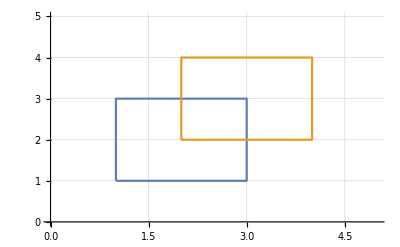

```mathematica
squarePoints={{1,1},{1,3},{3,3},{3,1},{1,1}};ListLinePlot[{squarePoints,(Ta1[1][#]&/@squarePoints)/.{l->1,k->1}},GridLines->Automatic,Axes->True,PlotRange->{{0,5},{0,5}}]
```

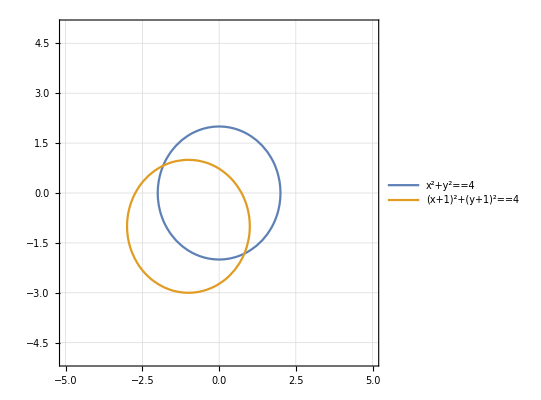

```mathematica
Show[
ContourPlot[{x^2+y^2==4,(((Ta1[1][{x,y}])⟦1⟧/.{l->1,k->1})^2+((Ta1[1][{x,y}])⟦2⟧/.{l->1,k->1})^2==4)},{x,-5,5},{y,-5,5},PlotLegends->"Expressions"],
GridLines->Automatic,Axes->True,PlotRange->{{-5,5},{-5,5}}
]
```

### Преобразование Лоренца

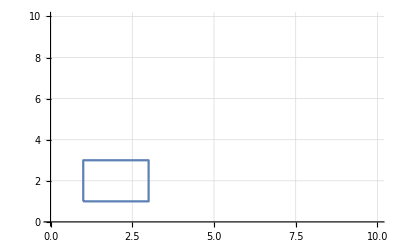

```mathematica
squarePoints={{1,1},{1,3},{3,3},{3,1},{1,1}};ListLinePlot[{squarePoints,Ta3[ⅈ][#]&/@squarePoints},GridLines->Automatic,Axes->True,PlotRange->{{0,10},{0,10}}]
```

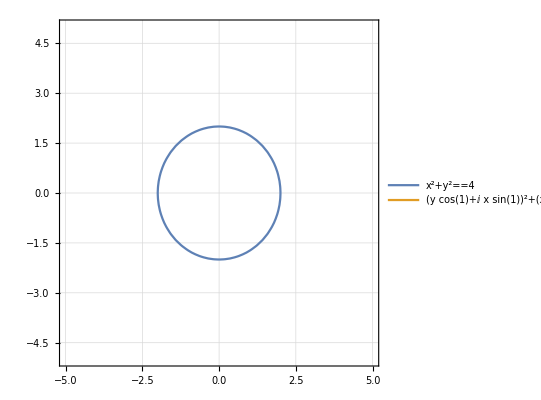

```mathematica
Show[
ContourPlot[{x^2+y^2==4,((Ta3[ⅈ][{x,y}])⟦1⟧)^2+((Ta3[ⅈ][{x,y}])⟦2⟧)^2==4},{x,-5,5},{y,-5,5},PlotLegends->"Expressions"],
GridLines->Automatic,Axes->True,PlotRange->{{-5,5},{-5,5}}
]
```

### Неоднородное растяжение

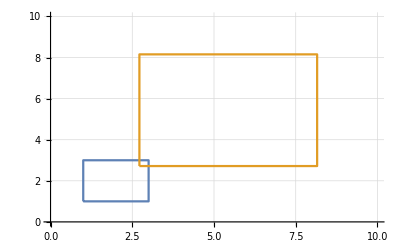

```mathematica
squarePoints={{1,1},{1,3},{3,3},{3,1},{1,1}};ListLinePlot[{squarePoints,(Ta6[1][#]&/@squarePoints)/.{k->1}},GridLines->Automatic,Axes->True,PlotRange->{{0,10},{0,10}}]
```

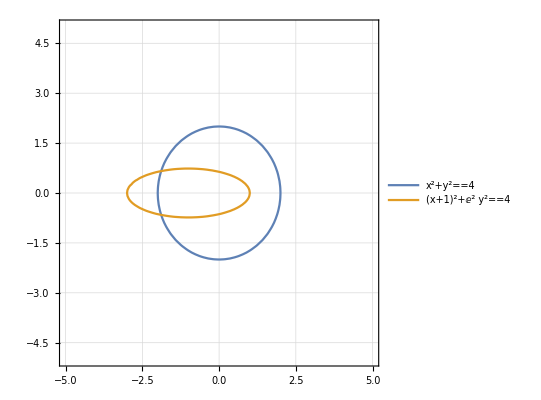

```mathematica
Show[
ContourPlot[{x^2+y^2==4,(((Ta1[1][{x,y}])⟦1⟧/.{l->1,k->1})^2+((Ta6[1][{x,y}])⟦2⟧/.{k->1})^2==4)},{x,-5,5},{y,-5,5},PlotLegends->"Expressions"],
GridLines->Automatic,Axes->True,PlotRange->{{-5,5},{-5,5}}
]
```